```mathematica
(* L1-norm calculation for a state under correlated PDC with memory: *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll[g,γ, μ,  p];

(* Defining uncorrelated-PDC Kraus Operators for single qubit: *)
C0=√(1-p) PauliMatrix[0];
C1=√p PauliMatrix[3];

(* Uncorrelated-PDC Kraus operators for two-qubits: *)
C00=KroneckerProduct[C0,C0];
C01=KroneckerProduct[C0,C1];
C10=KroneckerProduct[C1,C0];
C11=KroneckerProduct[C1,C1];

(* Correlated-PDC Kraus operators for two qubits: *)
D00 =√(1-p) KroneckerProduct[PauliMatrix[0],PauliMatrix[0]];
D11=√p KroneckerProduct[PauliMatrix[3],PauliMatrix[3]];

(* Checking the completeness of the Kraus operators: *)
c={C00,C01,C10,C11};
d={D00,D11};
FullSimplify[Sum[Transpose[c[[i]]].c[[i]],{i,1,4}]]//MatrixForm;
FullSimplify[Sum[Transpose[d[[i]]].d[[i]],{i,1,2}]]//MatrixForm;
```

```mathematica
(* MEMS-state density Matrix *)
ClearAll[g,γ,p,μ];
 ρ={{g,0,0,γ/2},{0,1-2g,0,0},{0,0,0,0},{γ/2,0,0,g}};
ρ//MatrixForm;
Tr[ρ];

(* Density Matrix after evolution in PDC: *)
 ρ2=(1-μ)*Sum[c[[i]].ρ.Transpose[c[[i]]],{i,1,4}]+μ*Sum[d[[i]].ρ.Transpose[d[[i]]],{i,1,2}]; 
Simplify[Tr[ρ2]];
ρ2//MatrixForm;
```

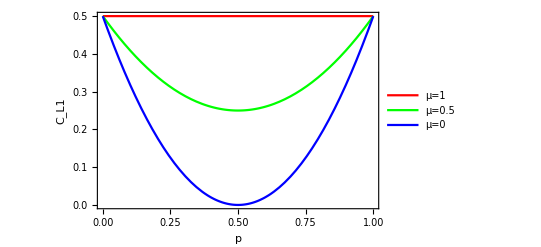

```mathematica
(* L1-norm of coherence: γ < 2/3 *)
ClearAll[g,γ, μ,  p];
γ=1/2;
g=1/3;
L1=Sum[If[i!=j,Abs[ρ2[[i,j]]],0],{i,1,4},{j,1,4}];

L1fig1=Plot[Evaluate@Table[L1,{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","C_L1"},PlotLegends->Placed[{"μ=1", "μ=0.5","μ=0"},{0.9,0.2}],PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]

Export["L1fig1_PDC.pdf",L1fig1];
```

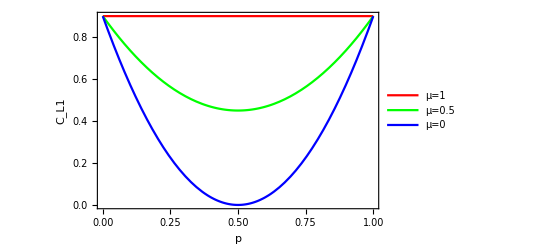

```mathematica
(*L1-norm of coherence: γ > 2/3 *)
ClearAll[g,γ, μ,  p];
γ=0.9;
g=γ/2;

L1=Sum[If[i!=j,Abs[ρ2[[i,j]]],0],{i,1,4},{j,1,4}];

L1fig2=Plot[Evaluate@Table[L1,{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","C_L1"},PlotLegends->Placed[{"μ=1", "μ=0.5","μ=0"},{0.9,0.2}],PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]

Export["L1fig2_PDC.pdf",L1fig2];
```

```mathematica
(* L1-norm plot in 3D: *)
ClearAll[g,γ,μ,p]
γ=0.5;
g=1/3;
L1norm3D=Plot3D[L1,{p,0,1},{μ,0,1},PlotRange->All,LabelStyle->Directive[Bold, Medium],AxesLabel->{" p"," μ","C_L1 "},ColorFunction->Function[{x,y,z},Hue[Mod[z,1]]],ColorFunctionScaling->False]
Export["L1norm3D_PDC.pdf",L1norm3D];
```

-Graphics3D-

```mathematica
(* Concurrence Module: *)
rhotilde[state_]:=(KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]).(Conjugate[state].(KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]));
  rhocon[state_]:=state.rhotilde[state];
eigensqrt[state_]:=Re[Sqrt[Eigenvalues[rhocon[state]]]];
order[state_]:=Sort[eigensqrt[state],Greater];
concurr[state_]:=Max[0,order[state][[1]]-order[state][[2]]-order[state][[3]]-order[state][[4]]];
```

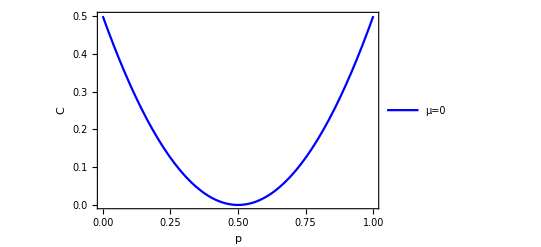

```mathematica
ClearAll[g,γ,μ,p]
γ=0.5;
g=1/3;
μ=0;
p1=Plot[concurr[ρ2],{p,0,1},PlotRange->All,Frame->True,FrameLabel->{"p","C"},PlotLegends->Placed[{"μ=0"},{0.9,0.1}],LabelStyle->Directive[Bold, Medium],PlotStyle->Blue]
```

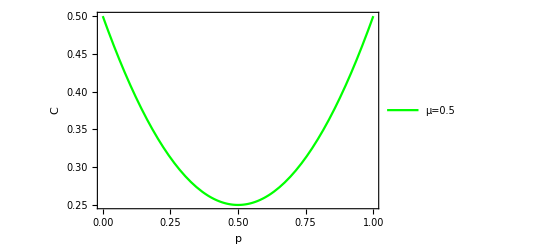

```mathematica
ClearAll[g,γ,μ,p]
γ=0.5;
g=1/3;
μ=0.5;
p2=Plot[concurr[ρ2],{p,0,1},PlotRange->All,Frame->True,FrameLabel->{"p","C"},PlotLegends->Placed[{"μ=0.5"},{0.9,0.2}],LabelStyle->Directive[Bold, Medium],PlotStyle->Green]
```

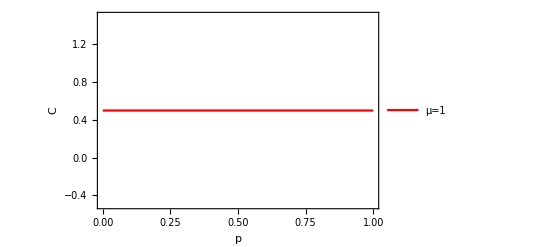

```mathematica
ClearAll[g,γ,μ,p]
γ=0.5;
g=1/3;
μ=1;
p3=Plot[concurr[ρ2],{p,0,1},PlotRange->All,Frame->True,FrameLabel->{"p","C"},PlotLegends->Placed[{"μ=1"},{0.9,0.3}],LabelStyle->Directive[Bold, Medium],PlotStyle->Red]
```

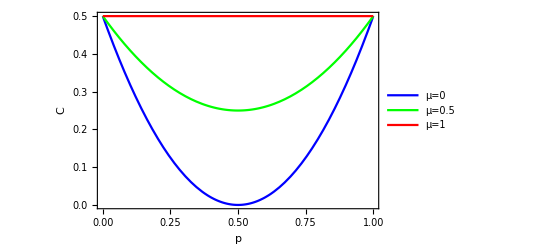

```mathematica
p4=Show[p1,p2,p3]
Export["Conc_PDC.pdf", p4];
```

```mathematica
(* Concurrence plot 3D: *)
ClearAll[g,γ,μ,p]
γ=0.5;
g=1/3;
Conc3D=Plot3D[concurr[ρ2],{p,0,1},{μ,0,1},PlotRange->All,LabelStyle->Directive[Bold, Medium],AxesLabel->{" p"," μ","C "},ColorFunction->Function[{x,y,z},Hue[Mod[z,1]]],ColorFunctionScaling->False]
Export["Conc3D_PDC.pdf",Conc3D];
```

-Graphics3D-

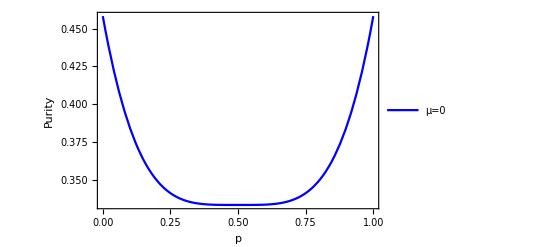

```mathematica
(* Purity Plots: 2D *)
ClearAll[g,γ,μ,p]
γ=0.5;
g=1/3;
μ=0;
f1=Plot[Tr[ρ2.ρ2],{p,0,1},PlotRange->All,Frame->True,FrameLabel->{"p","Purity"},PlotLegends->Placed[{"μ=0"},{0.9,0.1}],LabelStyle->Directive[Bold, Medium],PlotStyle->Blue]
```

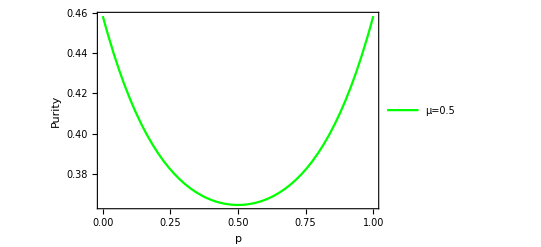

```mathematica
ClearAll[g,γ,μ,p]
γ=0.5;
g=1/3;
μ=0.5;
f2=Plot[Tr[ρ2.ρ2],{p,0,1},PlotRange->All,Frame->True,FrameLabel->{"p","Purity"},PlotRange->All,PlotLegends->Placed[{"μ=0.5"},{0.9,0.2}],LabelStyle->Directive[Bold, Medium],PlotStyle->Green]
```

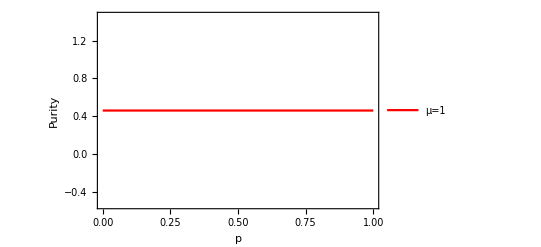

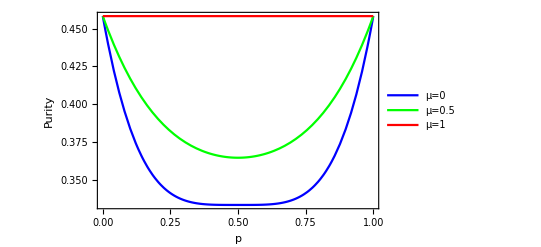

```mathematica
ClearAll[g,γ,μ,p]
γ=0.5;
g=1/3;
μ=1;
f3=Plot[Tr[ρ2.ρ2],{p,0,1},PlotRange->All,Frame->True,FrameLabel->{"p","Purity"},PlotLegends->Placed[{"μ=1"},{0.9,0.3}],LabelStyle->Directive[Bold, Medium],PlotStyle->Red]

f4=Show[f1,f2,f3]
Export["Conc_PDC.pdf", p4];
```

```mathematica
(* Purity plot in 3D: *)
ClearAll[g,γ,μ,p]
γ=0.5;
g=1/3;
Purity3D=Plot3D[Tr[ρ2.ρ2],{p,0,1},{μ,0,1},PlotRange->All,LabelStyle->Directive[Bold, Medium],AxesLabel->{" p"," μ","Purity  "},ColorFunction->Function[{x,y,z},Hue[Mod[z,1]]],ColorFunctionScaling->False]
(* ColorFunction->Function[{x,y,z},Hue[z]], *)
Export["Purity3D_PDC.pdf",Purity3D];
```

-Graphics3D-